```mathematica
(* Physical Constants *)
θ=28.1938 Degree;(* Weinberg Angle:28.18 Degree *)
ϕ=0;(* Z-Z' Mixing Angle: 10^-4 *)
GF=1.166578 10^(-11); (* Fermi Weak Constant [MeV]*)
MZ=91.188 10^3; (* Z Boson Mass [MeV] *)
MW=MZ Cos[θ]; (* W Boson Mass [MeV] *)
g=0.652879; (* Weak coupling *)
m=0.511; (* Electron mass *)
MZp=MZ; (* Z' Boson Mass *)
gp=0;(* U(1)B-L coupling *)
```

```mathematica
𝒶=1/137.036; (* QED fine structure *)
ℯ=Sqrt[4 Pi 𝒶]; (* Electronic charge *)
μB=ℯ/(2m) ; (* Bohr Magneton *)
μ=m; (* Electron/Positron Chemical Potential *)
T1=0.3; (* Plasma Temperature 1 [MeV] *)
T2=0.4; (* Plasma Temperature 2 [MeV] *)
T3=0.5; (* Plasma Temperature 3 [MeV] *)
α1=m/T1; 
β1=μ/T1;
α2=m/T2; 
β2=μ/T2;
α3=m/T3; 
β3=μ/T3;
```

```mathematica
(* Neutrino EM properties*)
ℯv=0;(*8.36 10^-8 ℯ*)
𝓇=0;(*51.4 10^-31 (5.067 10)^2*)
𝓊=0;(*3.08 10^-8 μB*)
```

```mathematica
(* Electron and Neutrino Isospin and Charge *)
Qe=-1;
Te=-1/2;
Qv=ℯv;(* ℯv *)
Tv=1/2;
```

```mathematica
(* Electron Boson Coupling  *)
gVe=Te Cos[ϕ]-2Qe Sin[θ]^2Cos[ϕ]+2gp/g Cos[θ]Sin[ϕ] ;
gAe=Te Cos[ϕ];
(* prime *)
gVep=-Te Sin[ϕ]-2Qe Sin[θ]^2Sin[ϕ]+2gp/g Cos[θ]Cos[ϕ]; 
gAep=-Te Sin[ϕ];
(* Neutrino Boson Coupling  *)
gVv=Tv Cos[ϕ]-2Qv Sin[θ]^2Cos[ϕ]+2gp/g Cos[θ]Sin[ϕ] ;
gAv=Tv Cos[ϕ];
(* prime *)
gVvp=-Tv Sin[ϕ]-2Qv Sin[θ]^2Sin[ϕ]+2gp/g Cos[θ]Cos[ϕ];
gAvp=-Tv Sin[ϕ];
```

```mathematica
(* CV and CA - SM Coupling *)
CVmut=gVe+Sqrt[2]Pi 𝒶 𝓇/(3GF); (*gVe+Sqrt[2]Pi αe 𝓇ν/(3GF)*)
CAmut=gAe;
CVe=CVmut+1;
CAe=CAmut+1;
```

```mathematica
(* Fermi Integral *)
Gp1[n_]:=1/(α1^(3+2 n))NIntegrate[x^(2n+1)Sqrt[x^2-α1^2]/(1+Exp[x+ β1]),{x,α1,Infinity}] ;
Gm1[n_]:=1/(α1^(3+2 n))NIntegrate[x^(2n+1)Sqrt[x^2-α1^2]/(1+Exp[x- β1]),{x,α1,Infinity}] ;
Gp2[n_]:=1/(α2^(3+2 n))NIntegrate[x^(2n+1)Sqrt[x^2-α2^2]/(1+Exp[x+ β2]),{x,α2,Infinity}] ;
Gm2[n_]:=1/(α2^(3+2 n))NIntegrate[x^(2n+1)Sqrt[x^2-α2^2]/(1+Exp[x- β2]),{x,α2,Infinity}] ;
Gp3[n_]:=1/(α3^(3+2 n))NIntegrate[x^(2n+1)Sqrt[x^2-α3^2]/(1+Exp[x+ β3]),{x,α3,Infinity}] ;
Gm3[n_]:=1/(α3^(3+2 n))NIntegrate[x^(2n+1)Sqrt[x^2-α3^2]/(1+Exp[x- β3]),{x,α3,Infinity}] ;
```

```mathematica
(*R,Q J *)
```

```mathematica
(*R1-----*)
```

```mathematica
RBSMe1=GF^2 m^8/(18 Pi^5 MZp^4)((MZp^4 CAe^2+2 MZ^4 gAep^2(gAvp^2+gVvp^2) + 2MZ^2 MZp^2CAe gAep (gAvp+gVvp))(4Gm1[1/2]Gp1[1/2]-Gm1[1/2]Gp1[-1/2]-Gm1[-1/2]Gp1[1/2]-2Gm1[-1/2]Gp1[-1/2])+(MZp^4 CVe^2+2 MZ^4 gVep^2 (gAvp^2+gVvp^2)+ 2MZ^2 MZp^2 CVe gVep(gAvp+gVvp))(4Gm1[1/2]Gp1[1/2]-Gm1[1/2]Gp1[-1/2]-Gm1[-1/2]Gp1[1/2]+9Gm1[0]Gp1[0]+7Gm1[-1/2]Gp1[-1/2]));
```

```mathematica
RBSMmut1=GF^2 m^8/(18 Pi^5 MZp^4)((MZp^4 CAmut^2+2 MZ^4 gAep^2(gAvp^2+gVvp^2) + 2MZ^2 MZp^2CAmut gAep (gAvp+gVvp))(4Gm1[1/2]Gp1[1/2]-Gm1[1/2]Gp1[-1/2]-Gm1[-1/2]Gp1[1/2]-2Gm1[-1/2]Gp1[-1/2])+(MZp^4 CVmut^2+2 MZ^4 gVep^2 (gAvp^2+gVvp^2)+ 2MZ^2 MZp^2 CVmut gVep(gAvp+gVvp))(4Gm1[1/2]Gp1[1/2]-Gm1[1/2]Gp1[-1/2]-Gm1[-1/2]Gp1[1/2]+9Gm1[0]Gp1[0]+7Gm1[-1/2]Gp1[-1/2]));
```

```mathematica
RMilie1=( GF Sqrt[2] 𝒶 ℯv m^6)/(3Pi^4 MZp^2) (CVe MZp^2+MZ^2 gVep(gAvp+gVvp))(Gm1[0]Gp1[0] +2Gm1[-1/2]Gp1[-1/2]);
```

```mathematica
RMilimut1=( GF Sqrt[2] 𝒶 ℯv m^6)/(3Pi^4 MZp^2) (CVmut MZp^2+MZ^2 gVep(gAvp+gVvp))(Gm1[0]Gp1[0] +2Gm1[-1/2]Gp1[-1/2]);
```

```mathematica
RMiu1=(𝒶^2 𝓊^2m^6)/(6 Pi^3)(Gm1[0]Gp1[0] +2Gm1[-1/2]Gp1[-1/2]);
```

```mathematica
(*F2---*)
RBSMe2=GF^2 m^8/(18 Pi^5 MZp^4)((MZp^4 CAe^2+2 MZ^4 gAep^2(gAvp^2+gVvp^2) + 2MZ^2 MZp^2CAe gAep (gAvp+gVvp))(4Gm2[1/2]Gp2[1/2]-Gm2[1/2]Gp2[-1/2]-Gm2[-1/2]Gp2[1/2]-2Gm2[-1/2]Gp2[-1/2])+(MZp^4 CVe^2+2 MZ^4 gVep^2 (gAvp^2+gVvp^2)+ 2MZ^2 MZp^2 CVe gVep(gAvp+gVvp))(4Gm2[1/2]Gp2[1/2]-Gm2[1/2]Gp2[-1/2]-Gm2[-1/2]Gp2[1/2]+9Gm2[0]Gp2[0]+7Gm2[-1/2]Gp2[-1/2]));
```

```mathematica
RBSMmut2=GF^2 m^8/(18 Pi^5 MZp^4)((MZp^4 CAmut^2+2 MZ^4 gAep^2(gAvp^2+gVvp^2) + 2MZ^2 MZp^2CAmut gAep (gAvp+gVvp))(4Gm2[1/2]Gp2[1/2]-Gm2[1/2]Gp2[-1/2]-Gm2[-1/2]Gp2[1/2]-2Gm2[-1/2]Gp2[-1/2])+(MZp^4 CVmut^2+2 MZ^4 gVep^2 (gAvp^2+gVvp^2)+ 2MZ^2 MZp^2 CVmut gVep(gAvp+gVvp))(4Gm2[1/2]Gp2[1/2]-Gm2[1/2]Gp2[-1/2]-Gm2[-1/2]Gp2[1/2]+9Gm2[0]Gp2[0]+7Gm2[-1/2]Gp2[-1/2]));
```

```mathematica
RMilie2=(GF Sqrt[2] 𝒶 ℯv m^6)/(3Pi^4 MZp^2) (CVe MZp^2+MZ^2 gVep(gAvp+gVvp))(Gm2[0]Gp2[0] +2Gm2[-1/2]Gp2[-1/2]);
```

```mathematica
RMilimut2=(GF Sqrt[2] 𝒶 ℯv m^6)/(3Pi^4 MZp^2) (CVmut MZp^2+MZ^2 gVep(gAvp+gVvp))(Gm2[0]Gp2[0] +2Gm2[-1/2]Gp2[-1/2]);
```

```mathematica
RMiu2=(𝒶^2 𝓊^2m^6)/(6 Pi^3)(Gm2[0]Gp2[0] +2Gm2[-1/2]Gp2[-1/2]);
```

```mathematica
(*F3---*)
```

```mathematica
RBSMe3=GF^2 m^8/(18 Pi^5 MZp^4)((MZp^4 CAe^2+2 MZ^4 gAep^2(gAvp^2+gVvp^2) + 2MZ^2 MZp^2CAe gAep (gAvp+gVvp))(4Gm3[1/2]Gp3[1/2]-Gm3[1/2]Gp3[-1/2]-Gm3[-1/2]Gp3[1/2]-2Gm3[-1/2]Gp3[-1/2])+(MZp^4 CVe^2+2 MZ^4 gVep^2 (gAvp^2+gVvp^2)+ 2MZ^2 MZp^2 CVe gVep(gAvp+gVvp))(4Gm3[1/2]Gp3[1/2]-Gm3[1/2]Gp3[-1/2]-Gm3[-1/2]Gp3[1/2]+9Gm3[0]Gp3[0]+7Gm3[-1/2]Gp3[-1/2]));
```

```mathematica
RBSMmut3=GF^2 m^8/(18 Pi^5 MZp^4)((MZp^4 CAmut^2+2 MZ^4 gAep^2(gAvp^2+gVvp^2) + 2MZ^2 MZp^2CAmut gAep (gAvp+gVvp))(4Gm3[1/2]Gp3[1/2]-Gm3[1/2]Gp3[-1/2]-Gm3[-1/2]Gp3[1/2]-2Gm3[-1/2]Gp3[-1/2])+(MZp^4 CVmut^2+2 MZ^4 gVep^2 (gAvp^2+gVvp^2)+ 2MZ^2 MZp^2 CVmut gVep(gAvp+gVvp))(4Gm3[1/2]Gp3[1/2]-Gm3[1/2]Gp3[-1/2]-Gm3[-1/2]Gp3[1/2]+9Gm3[0]Gp3[0]+7Gm3[-1/2]Gp3[-1/2]));
```

```mathematica
RMilie3=( GF Sqrt[2] 𝒶 ℯv m^6)/(3Pi^4 MZp^2) (CVe MZp^2+MZ^2 gVep(gAvp+gVvp))(Gm3[0]Gp3[0] +2Gm3[-1/2]Gp3[-1/2]);
```

```mathematica
RMilimut3=(GF Sqrt[2] 𝒶 ℯv m^6)/(3Pi^4 MZp^2) (CVmut MZp^2+MZ^2 gVep(gAvp+gVvp))(Gm3[0]Gp3[0] +2Gm3[-1/2]Gp3[-1/2]);
```

```mathematica
RMiu3=(𝒶^2 𝓊^2m^6)/(6 Pi^3)(Gm3[0]Gp3[0] +2Gm3[-1/2]Gp3[-1/2]);
```

```mathematica
(*-------------------*)
```

```mathematica
(*Q-----*)
```

```mathematica
(*Q1-----*)
```

```mathematica
QBSMe1=GF^2 m^9/(18 Pi^5 MZp^4)((MZp^4 CAe^2+2 MZ^4 gAep^2(gAvp^2+gVvp^2) + 2MZ^2 MZp^2CAe gAep (gAvp+gVvp))(4Gm1[1]Gp1[1/2]+4Gm1[1/2]Gp1[1]-Gm1[1]Gp1[-1/2]-Gm1[-1/2]Gp1[1]-Gm1[1/2]Gp1[0]-Gm1[0]Gp1[1/2]-2Gm1[0]Gp1[-1/2]-2Gm1[-1/2]Gp1[0])+(MZp^4 CVe^2+2 MZ^4 gVep^2 (gAvp^2+gVvp^2)+ 2MZ^2 MZp^2 CVe gVep(gAvp+gVvp))(4Gm1[1]Gp1[1/2]+4Gm1[1/2]Gp1[1]-Gm1[1]Gp1[-1/2]-Gm1[-1/2]Gp1[1]+8 Gm1[1/2]Gp1[0]+8Gm1[0]Gp1[1/2]+7Gm1[0]Gp1[-1/2]+7Gm1[-1/2]Gp1[0]));
```

```mathematica
QBSMmut1=GF^2 m^9/(18 Pi^5 MZp^4)((MZp^4 CAmut^2+2 MZ^4 gAep^2(gAvp^2+gVvp^2) + 2MZ^2 MZp^2CAmut gAep (gAvp+gVvp))(4Gm1[1]Gp1[1/2]+4Gm1[1/2]Gp1[1]-Gm1[1]Gp1[-1/2]-Gm1[-1/2]Gp1[1]-Gm1[1/2]Gp1[0]-Gm1[0]Gp1[1/2]-2Gm1[0]Gp1[-1/2]-2Gm1[-1/2]Gp1[0])+(MZp^4 CVmut^2+2 MZ^4 gVep^2 (gAvp^2+gVvp^2)+ 2MZ^2 MZp^2 CVmut gVep(gAvp+gVvp))(4Gm1[1]Gp1[1/2]+4Gm1[1/2]Gp1[1]-Gm1[1]Gp1[-1/2]-Gm1[-1/2]Gp1[1]+8 Gm1[1/2]Gp1[0]+8Gm1[0]Gp1[1/2]+7Gm1[0]Gp1[-1/2]+7Gm1[-1/2]Gp1[0]));
```

```mathematica
QMilie1=(GF Sqrt[2] 𝒶 ℯv m^7)/(3Pi^4 MZp^2) (CVe MZp^2+MZ^2 gVep(gAvp+gVvp))(Gm1[1/2]Gp1[0]+Gm1[0]Gp1[1/2] +2Gm1[0]Gp1[-1/2]+2Gm1[-1/2]Gp1[0]);
```

```mathematica
QMilimut1=(GF Sqrt[2] 𝒶 ℯv m^7)/(3Pi^4 MZp^2) (CVmut MZp^2+MZ^2 gVep(gAvp+gVvp))(Gm1[1/2]Gp1[0]+Gm1[0]Gp1[1/2] +2Gm1[0]Gp1[-1/2]+2Gm1[-1/2]Gp1[0]);
```

```mathematica
QMiu1=(𝒶^2 𝓊^2m^7)/(6 Pi^3)(Gm1[1/2]Gp1[0]+Gm1[0]Gp1[1/2] +2Gm1[0]Gp1[-1/2]+2Gm1[-1/2]Gp1[0]);
```

```mathematica
(*Q2-----*)
```

```mathematica
QBSMe2=GF^2 m^9/(18 Pi^5 MZp^4)((MZp^4 CAe^2+2 MZ^4 gAep^2(gAvp^2+gVvp^2) + 2MZ^2 MZp^2CAe gAep (gAvp+gVvp))(4Gm2[1]Gp2[1/2]+4Gm2[1/2]Gp2[1]-Gm2[1]Gp2[-1/2]-Gm2[-1/2]Gp2[1]-Gm2[1/2]Gp2[0]-Gm2[0]Gp2[1/2]-2Gm2[0]Gp2[-1/2]-2Gm2[-1/2]Gp2[0])+(MZp^4 CVe^2+2 MZ^4 gVep^2 (gAvp^2+gVvp^2)+ 2MZ^2 MZp^2 CVe gVep(gAvp+gVvp))(4Gm2[1]Gp2[1/2]+4Gm2[1/2]Gp2[1]-Gm2[1]Gp2[-1/2]-Gm2[-1/2]Gp2[1]+8 Gm2[1/2]Gp2[0]+8Gm2[0]Gp2[1/2]+7Gm2[0]Gp2[-1/2]+7Gm2[-1/2]Gp2[0]));
```

```mathematica
QBSMmut2=GF^2 m^9/(18 Pi^5 MZp^4)((MZp^4 CAmut^2+2 MZ^4 gAep^2(gAvp^2+gVvp^2) + 2MZ^2 MZp^2CAmut gAep (gAvp+gVvp))(4Gm2[1]Gp2[1/2]+4Gm2[1/2]Gp2[1]-Gm2[1]Gp2[-1/2]-Gm2[-1/2]Gp2[1]-Gm2[1/2]Gp2[0]-Gm2[0]Gp2[1/2]-2Gm2[0]Gp2[-1/2]-2Gm2[-1/2]Gp2[0])+(MZp^4 CVmut^2+2 MZ^4 gVep^2 (gAvp^2+gVvp^2)+ 2MZ^2 MZp^2 CVmut gVep(gAvp+gVvp))(4Gm2[1]Gp2[1/2]+4Gm2[1/2]Gp2[1]-Gm2[1]Gp2[-1/2]-Gm2[-1/2]Gp2[1]+8 Gm2[1/2]Gp2[0]+8Gm2[0]Gp2[1/2]+7Gm2[0]Gp2[-1/2]+7Gm2[-1/2]Gp2[0]));
```

```mathematica
QMilie2=(GF Sqrt[2] 𝒶 ℯv m^7)/(3Pi^4 MZp^2) (CVe MZp^2+MZ^2 gVep(gAvp+gVvp))(Gm2[1/2]Gp2[0]+Gm2[0]Gp2[1/2] +2Gm2[0]Gp2[-1/2]+2Gm2[-1/2]Gp2[0]);
```

```mathematica
QMilimut2=(GF Sqrt[2] 𝒶 ℯv m^7)/(3Pi^4 MZp^2) (CVmut MZp^2+MZ^2 gVep(gAvp+gVvp))(Gm2[1/2]Gp2[0]+Gm2[0]Gp2[1/2] +2Gm2[0]Gp2[-1/2]+2Gm2[-1/2]Gp2[0]);
```

```mathematica
QMiu2=(𝒶^2 𝓊^2m^7)/(6 Pi^3)(Gm2[1/2]Gp2[0]+Gm2[0]Gp2[1/2] +2Gm2[0]Gp2[-1/2]+2Gm2[-1/2]Gp2[0]);
```

```mathematica
(*Q3-----*)
```

```mathematica
QBSMe3=GF^2 m^9/(18 Pi^5 MZp^4)((MZp^4 CAe^2+2 MZ^4 gAep^2(gAvp^2+gVvp^2) + 2MZ^2 MZp^2CAe gAep (gAvp+gVvp))(4Gm3[1]Gp3[1/2]+4Gm3[1/2]Gp3[1]-Gm3[1]Gp3[-1/2]-Gm3[-1/2]Gp3[1]-Gm3[1/2]Gp3[0]-Gm3[0]Gp3[1/2]-2Gm3[0]Gp3[-1/2]-2Gm3[-1/2]Gp3[0])+(MZp^4 CVe^2+2 MZ^4 gVep^2 (gAvp^2+gVvp^2)+ 2MZ^2 MZp^2 CVe gVep(gAvp+gVvp))(4Gm3[1]Gp3[1/2]+4Gm3[1/2]Gp3[1]-Gm3[1]Gp3[-1/2]-Gm3[-1/2]Gp3[1]+8 Gm3[1/2]Gp3[0]+8Gm3[0]Gp3[1/2]+7Gm3[0]Gp3[-1/2]+7Gm3[-1/2]Gp3[0]));
```

```mathematica
QBSMmut3=GF^2 m^9/(18 Pi^5 MZp^4)((MZp^4 CAmut^2+2 MZ^4 gAep^2(gAvp^2+gVvp^2) + 2MZ^2 MZp^2CAmut gAep (gAvp+gVvp))(4Gm3[1]Gp3[1/2]+4Gm3[1/2]Gp3[1]-Gm3[1]Gp3[-1/2]-Gm3[-1/2]Gp3[1]-Gm3[1/2]Gp3[0]-Gm3[0]Gp3[1/2]-2Gm3[0]Gp3[-1/2]-2Gm3[-1/2]Gp3[0])+(MZp^4 CVmut^2+2 MZ^4 gVep^2 (gAvp^2+gVvp^2)+ 2MZ^2 MZp^2 CVmut gVep(gAvp+gVvp))(4Gm3[1]Gp3[1/2]+4Gm3[1/2]Gp3[1]-Gm3[1]Gp3[-1/2]-Gm3[-1/2]Gp3[1]+8 Gm3[1/2]Gp3[0]+8Gm3[0]Gp3[1/2]+7Gm3[0]Gp3[-1/2]+7Gm3[-1/2]Gp3[0]));
```

```mathematica
QMilie3=(GF Sqrt[2] 𝒶 ℯv m^7)/(3Pi^4 MZp^2) (CVe MZp^2+MZ^2 gVep(gAvp+gVvp))(Gm3[1/2]Gp3[0]+Gm3[0]Gp3[1/2] +2Gm3[0]Gp3[-1/2]+2Gm3[-1/2]Gp3[0]);
```

```mathematica
QMilimut3=(GF Sqrt[2] 𝒶 ℯv m^7)/(3Pi^4 MZp^2) (CVmut MZp^2+MZ^2 gVep(gAvp+gVvp))(Gm3[1/2]Gp3[0]+Gm3[0]Gp3[1/2] +2Gm3[0]Gp3[-1/2]+2Gm3[-1/2]Gp3[0]);
```

```mathematica
QMiu3=(𝒶^2 𝓊^2m^7)/(6 Pi^3)(Gm3[1/2]Gp3[0]+Gm3[0]Gp3[1/2] +2Gm3[0]Gp3[-1/2]+2Gm3[-1/2]Gp3[0]);
```

```mathematica
(*-------------------*)
```

```mathematica
(*J-----*)
```

```mathematica
(*J1-----*)
```

```mathematica
JBSMe1=GF^2m^10/(18 Pi^5 MZp^4)((MZp^4 CAe^2+2 MZ^4 gAep^2(gAvp^2+gVvp^2) + 2MZ^2 MZp^2CAe gAep (gAvp+gVvp))(4Gm1[3/2]Gp1[1/2]+4Gm1[1/2]Gp1[3/2]-Gm1[3/2]Gp1[-1/2]-Gm1[-1/2]Gp1[3/2]-2Gm1[1/2]Gp1[1/2]-2Gm1[1/2]Gp1[-1/2]-2Gm1[-1/2]Gp1[1/2])+(MZp^4 CVe^2+2 MZ^4 gVep^2 (gAvp^2+gVvp^2)+ 2MZ^2 MZp^2 CVe gVep(gAvp+gVvp))(4Gm1[3/2]Gp1[1/2]+4Gm1[1/2]Gp1[3/2]-Gm1[3/2]Gp1[-1/2]-Gm1[-1/2]Gp1[3/2]+9 Gm1[1]Gp1[0]+9Gm1[0]Gp1[1]-2Gm1[1/2]Gp1[1/2]+7Gm1[1/2]Gp1[-1/2]+7Gm1[-1/2]Gp1[1/2]));
```

```mathematica
JBSMmut1=GF^2m^10/(18 Pi^5 MZp^4)((MZp^4 CAmut^2+2 MZ^4 gAep^2(gAvp^2+gVvp^2) + 2MZ^2 MZp^2CAmut gAep (gAvp+gVvp))(4Gm1[3/2]Gp1[1/2]+4Gm1[1/2]Gp1[3/2]-Gm1[3/2]Gp1[-1/2]-Gm1[-1/2]Gp1[3/2]-2Gm1[1/2]Gp1[1/2]-2Gm1[1/2]Gp1[-1/2]-2Gm1[-1/2]Gp1[1/2])+(MZp^4 CVmut^2+2 MZ^4 gVep^2 (gAvp^2+gVvp^2)+ 2MZ^2 MZp^2 CVmut gVep(gAvp+gVvp))(4Gm1[3/2]Gp1[1/2]+4Gm1[1/2]Gp1[3/2]-Gm1[3/2]Gp1[-1/2]-Gm1[-1/2]Gp1[3/2]+9 Gm1[1]Gp1[0]+9Gm1[0]Gp1[1]-2Gm1[1/2]Gp1[1/2]+7Gm1[1/2]Gp1[-1/2]+7Gm1[-1/2]Gp1[1/2]));
```

```mathematica
JMilie1=(GF Sqrt[2] 𝒶 ℯv m^8)/(3Pi^4 MZp^2) (CVe MZp^2+MZ^2 gVep(gAvp+gVvp))(Gm1[1]Gp1[0]+Gm1[0]Gp1[1] +2Gm1[1/2]Gp1[-1/2]+2Gm1[-1/2]Gp1[1/2]);
```

```mathematica
JMilimut1=(GF Sqrt[2] 𝒶 ℯv m^8)/(3Pi^4 MZp^2) (CVmut MZp^2+MZ^2 gVep(gAvp+gVvp))(Gm1[1]Gp1[0]+Gm1[0]Gp1[1] +2Gm1[1/2]Gp1[-1/2]+2Gm1[-1/2]Gp1[1/2]);
```

```mathematica
JMiu1=(𝒶^2 𝓊^2m^8)/(6 Pi^3)(Gm1[1]Gp1[0]+Gm1[0]Gp1[1] +2Gm1[1/2]Gp1[-1/2]+2Gm1[-1/2]Gp1[1/2]);
```

```mathematica
(*J2-----*)
```

```mathematica
JBSMe2=GF^2m^10/(18 Pi^5 MZp^4)((MZp^4 CAe^2+2 MZ^4 gAep^2(gAvp^2+gVvp^2) + 2MZ^2 MZp^2CAe gAep (gAvp+gVvp))(4Gm2[3/2]Gp2[1/2]+4Gm2[1/2]Gp2[3/2]-Gm2[3/2]Gp2[-1/2]-Gm2[-1/2]Gp2[3/2]-2Gm2[1/2]Gp2[1/2]-2Gm2[1/2]Gp2[-1/2]-2Gm2[-1/2]Gp2[1/2])+(MZp^4 CVe^2+2 MZ^4 gVep^2 (gAvp^2+gVvp^2)+ 2MZ^2 MZp^2 CVe gVep(gAvp+gVvp))(4Gm2[3/2]Gp2[1/2]+4Gm2[1/2]Gp2[3/2]-Gm2[3/2]Gp2[-1/2]-Gm2[-1/2]Gp2[3/2]+9 Gm2[1]Gp2[0]+9Gm2[0]Gp2[1]-2Gm2[1/2]Gp2[1/2]+7Gm2[1/2]Gp2[-1/2]+7Gm2[-1/2]Gp2[1/2]));
```

```mathematica
JBSMmut2=GF^2m^10/(18 Pi^5 MZp^4)((MZp^4 CAmut^2+2 MZ^4 gAep^2(gAvp^2+gVvp^2) + 2MZ^2 MZp^2CAmut gAep (gAvp+gVvp))(4Gm2[3/2]Gp2[1/2]+4Gm2[1/2]Gp2[3/2]-Gm2[3/2]Gp2[-1/2]-Gm2[-1/2]Gp2[3/2]-2Gm2[1/2]Gp2[1/2]-2Gm2[1/2]Gp2[-1/2]-2Gm2[-1/2]Gp2[1/2])+(MZp^4 CVmut^2+2 MZ^4 gVep^2 (gAvp^2+gVvp^2)+ 2MZ^2 MZp^2 CVmut gVep(gAvp+gVvp))(4Gm2[3/2]Gp2[1/2]+4Gm2[1/2]Gp2[3/2]-Gm2[3/2]Gp2[-1/2]-Gm2[-1/2]Gp2[3/2]+9 Gm2[1]Gp2[0]+9Gm2[0]Gp2[1]-2Gm2[1/2]Gp2[1/2]+7Gm2[1/2]Gp2[-1/2]+7Gm2[-1/2]Gp2[1/2]));
```

```mathematica
JMilie2=(GF Sqrt[2] 𝒶 ℯv m^8)/(3Pi^4 MZp^2) (CVe MZp^2+MZ^2 gVep(gAvp+gVvp))(Gm2[1]Gp2[0]+Gm2[0]Gp2[1] +2Gm2[1/2]Gp2[-1/2]+2Gm2[-1/2]Gp2[1/2]);
```

```mathematica
JMilimut2=(GF Sqrt[2] 𝒶 ℯv m^8)/(3Pi^4 MZp^2) (CVmut MZp^2+MZ^2 gVep(gAvp+gVvp))(Gm2[1]Gp2[0]+Gm2[0]Gp2[1] +2Gm2[1/2]Gp2[-1/2]+2Gm2[-1/2]Gp2[1/2]);
```

```mathematica
JMiu2=(𝒶^2 𝓊^2m^8)/(6 Pi^3)(Gm2[1]Gp2[0]+Gm2[0]Gp2[1] +2Gm2[1/2]Gp2[-1/2]+2Gm2[-1/2]Gp2[1/2]);
```

```mathematica
(*J3-----*)
```

```mathematica
JBSMe3=GF^2m^10/(18 Pi^5 MZp^4)((MZp^4 CAe^2+2 MZ^4 gAep^2(gAvp^2+gVvp^2) + 2MZ^2 MZp^2CAe gAep (gAvp+gVvp))(4Gm3[3/2]Gp3[1/2]+4Gm3[1/2]Gp3[3/2]-Gm3[3/2]Gp3[-1/2]-Gm3[-1/2]Gp3[3/2]-2Gm3[1/2]Gp3[1/2]-2Gm3[1/2]Gp3[-1/2]-2Gm3[-1/2]Gp3[1/2])+(MZp^4 CVe^2+2 MZ^4 gVep^2 (gAvp^2+gVvp^2)+ 2MZ^2 MZp^2 CVe gVep(gAvp+gVvp))(4Gm3[3/2]Gp3[1/2]+4Gm3[1/2]Gp3[3/2]-Gm3[3/2]Gp3[-1/2]-Gm3[-1/2]Gp3[3/2]+9 Gm3[1]Gp3[0]+9Gm3[0]Gp3[1]-2Gm3[1/2]Gp3[1/2]+7Gm3[1/2]Gp3[-1/2]+7Gm3[-1/2]Gp3[1/2]));
```

```mathematica
JBSMmut3=GF^2m^10/(18 Pi^5 MZp^4)((MZp^4 CAmut^2+2 MZ^4 gAep^2(gAvp^2+gVvp^2) + 2MZ^2 MZp^2CAmut gAep (gAvp+gVvp))(4Gm3[3/2]Gp3[1/2]+4Gm3[1/2]Gp3[3/2]-Gm3[3/2]Gp3[-1/2]-Gm3[-1/2]Gp3[3/2]-2Gm3[1/2]Gp3[1/2]-2Gm3[1/2]Gp3[-1/2]-2Gm3[-1/2]Gp3[1/2])+(MZp^4 CVmut^2+2 MZ^4 gVep^2 (gAvp^2+gVvp^2)+ 2MZ^2 MZp^2 CVmut gVep(gAvp+gVvp))(4Gm3[3/2]Gp3[1/2]+4Gm3[1/2]Gp3[3/2]-Gm3[3/2]Gp3[-1/2]-Gm3[-1/2]Gp3[3/2]+9 Gm3[1]Gp3[0]+9Gm3[0]Gp3[1]-2Gm3[1/2]Gp3[1/2]+7Gm3[1/2]Gp3[-1/2]+7Gm3[-1/2]Gp3[1/2]));
```

```mathematica
JMilie3=(GF Sqrt[2] 𝒶 ℯv m^8)/(3Pi^4 MZp^2) (CVe MZp^2+MZ^2 gVep(gAvp+gVvp))(Gm3[1]Gp3[0]+Gm3[0]Gp3[1] +2Gm3[1/2]Gp3[-1/2]+2Gm3[-1/2]Gp3[1/2]);
```

```mathematica
JMilimut3=(GF Sqrt[2] 𝒶 ℯv m^8)/(3Pi^4 MZp^2) (CVmut MZp^2+MZ^2 gVep(gAvp+gVvp))(Gm3[1]Gp3[0]+Gm3[0]Gp3[1] +2Gm3[1/2]Gp3[-1/2]+2Gm3[-1/2]Gp3[1/2]);
```

```mathematica
JMiu3=(𝒶^2 𝓊^2m^8)/(6 Pi^3)(Gm3[1]Gp3[0]+Gm3[0]Gp3[1] +2Gm3[1/2]Gp3[-1/2]+2Gm3[-1/2]Gp3[1/2]);
```

```mathematica
(*-------------------*)
```

```mathematica
(*R,Q J -- Total*)
```

```mathematica
Rtotal1=RBSMe1+2RBSMmut1+RMilie1+2RMilimut1+RMiu1
```

2.27019×10^-28

```mathematica
Rtotal2=RBSMe2+2RBSMmut2+RMilie2+2RMilimut2+RMiu2
```

2.74236×10^-27

```mathematica
Rtotal3=RBSMe3+2RBSMmut3+RMilie3+2RMilimut3+RMiu3
```

1.78115×10^-26

```mathematica
(*-------------------*)
```

```mathematica
Qtotal1=QBSMe1+2QBSMmut1+QMilie1+2QMilimut1+QMiu1
```

6.17045×10^-28

```mathematica
Qtotal2=QBSMe2+2QBSMmut2+QMilie2+2QMilimut2+QMiu2
```

9.51559×10^-27

```mathematica
Qtotal3=QBSMe3+2QBSMmut3+QMilie3+2QMilimut3+QMiu3
```

7.56913×10^-26

```mathematica
(*-------------------*)
```

```mathematica
Jtotal1=JBSMe1+2JBSMmut1+JMilie1+2JMilimut1+JMiu1
```

9.79809×10^-28

```mathematica
Jtotal2=JBSMe2+2JBSMmut2+JMilie2+2JMilimut2+JMiu2
```

1.97078×10^-26

```mathematica
Jtotal3=JBSMe3+2JBSMmut3+JMilie3+2JMilimut3+JMiu3
```

1.94215×10^-25

```mathematica
(*Average Energy (E)and Average Secend Moment Energy (M)*)
```

```mathematica
(* Emisi=N[(2700 Zeta[5]T)/(7 Pi^4)] *)
```

```mathematica
Eavg1=Qtotal1/(2 Rtotal1)
```

1.35901

```mathematica
Eavg2=Qtotal2/( 2Rtotal2)
```

1.73493

```mathematica
Eavg3=Qtotal3/( 2Rtotal3)
```

2.12479

```mathematica
(* Mmisi=(2+dmisi)/(1+dmisi)Emisi^2 *)
```

```mathematica
Mavg1=Jtotal1/(2Rtotal1)
```

2.15799

```mathematica
Mavg2=Jtotal2/(2Rtotal2)
```

3.59322

```mathematica
Mavg3=Jtotal3/(2Rtotal3)
```

5.45195

```mathematica
(*-------*)
```

```mathematica
pinch1=Mavg1/Eavg1^2
```

1.16843

```mathematica
pinch2=Mavg2/Eavg2^2
```

1.19377

```mathematica
pinch3=Mavg3/Eavg3^2
```

1.20759

```mathematica
(*----*)
```

```mathematica
Clear[d1,d2,d3]
```

```mathematica
solved1=NSolve[pinch1==(2+d1)/(1+d1),d1]
```

{{d1→4.93734}}

```mathematica
solved2=NSolve[pinch2==(2+d2)/(1+d2),d2]
```

{{d2→4.16067}}

```mathematica
solved3=NSolve[pinch3==(2+d3)/(1+d3),d3]
```

{{d3→3.8171}}

```mathematica
d1=4.93734
```

4.93734

```mathematica
d2=4.16067
```

4.16067

```mathematica
d3=3.8171
```

3.8171

```mathematica
Ν1=(d1+1)^(d1+1)/Gamma[d1+1]
```

363.22

```mathematica
Ν2=(d2+1)^(d2+1)/Gamma[d2+1]
```

155.421

```mathematica
Ν3=(d3+1)^(d3+1)/Gamma[d3+1]
```

106.375

```mathematica
A=0.1425776426;a=1.018192299;dmisi=3.180657028;
```

```mathematica
Spectramisi1= A/T1 (x/T1)^dmisi Exp[-a x/T1]
```

21.879 ⅇ^(-3.39397 x) x^3.18066

```mathematica
Spectramisi2= A/T2 (x/T2)^dmisi Exp[-a x/T2]
```

6.57207 ⅇ^(-2.54548 x) x^3.18066

```mathematica
Spectramisi3= A/T3 (x/T3)^dmisi Exp[-a x/T3]
```

2.58556 ⅇ^(-2.03638 x) x^3.18066

```mathematica
Spectra1=Ν1 x^d1/(Eavg1)^(d1+1)Exp[-(d1+1)x/Eavg1]
```

58.7726 ⅇ^(-4.36886 x) x^4.93734

```mathematica
Spectra2=Ν2 x^d2/(Eavg2)^(d2+1)Exp[-(d2+1)x/Eavg2]
```

9.05019 ⅇ^(-2.97457 x) x^4.16067

```mathematica
Spectra3=Ν3 x^d3/(Eavg3)^(d3+1)Exp[-(d3+1)x/Eavg3]
```

2.81922 ⅇ^(-2.2671 x) x^3.8171

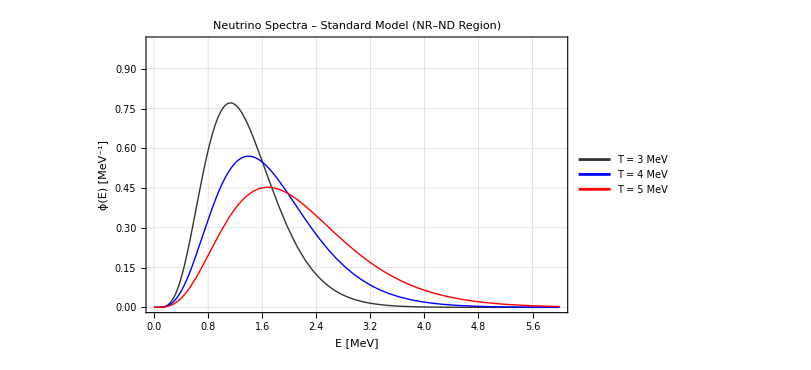

```mathematica
Plot[Evaluate[{Spectra1,Spectra2,Spectra3}],{x,0,6},PlotRange->{0,1},PlotLabel->Style["Neutrino Spectra – Standard Model (NR–ND Region)",Bold,16,GrayLevel[0.2]],AxesLabel->{"E (MeV)","ϕ(E)(MeV^-1)"},PlotLegends->Placed[{"T = 3 MeV","T = 4 MeV","T = 5 MeV"},Right],PlotStyle->{{Thick,GrayLevel[0.2]},{Thick,Blue},{Thick,Red}},Frame->True,FrameLabel->{Style["E [MeV]",14,FontFamily->"Times"],Style["ϕ(E) [MeV^-1]",14,FontFamily->"Times"]},BaseStyle->{FontFamily->"Times",FontSize->12},GridLines->Automatic,TicksStyle->Directive[GrayLevel[0.2],12],ImageSize->600]
```